```mathematica
T = l^2*m*(2*θ1dot^2 + 2*θ1dot*θ2dot*Cos[θ1-θ2] + θ2dot^2)/2;
U = -m*g*l*(2*Cos[θ1] + Cos[θ2]);

L = T - U;
vals = {θ1 -> θ1[t], θ2->θ2[t], θ1dot -> θ1'[t], θ2dot->θ2'[t]};

dLdtheta1 = D[L, θ1]/.vals;
dLdtheta1 = FullSimplify[dLdtheta1];
dLdtheta1dot = D[L, θ1dot]/.vals;
dLdtheta1dot = FullSimplify[dLdtheta1dot];
ddLdtheta1dotdt = FullSimplify[D[dLdtheta1dot, t]];
dLdtheta2 = D[L, θ2]/.vals;
dLdtheta2 = FullSimplify[dLdtheta2];
dLdtheta2dot = D[L, θ2dot]/.vals;
dLdtheta2dot = FullSimplify[dLdtheta2dot];
ddLdtheta2dotdt = FullSimplify[D[dLdtheta2dot, t]];

eq1 = dLdtheta1 - ddLdtheta1dotdt == 0;
eq1 = FullSimplify[eq1];

eq2 = dLdtheta2 - ddLdtheta2dotdt == 0;
eq2 = FullSimplify[eq2];
```

(5-t) (-9.8 Sin[ϕ[t]]+2 ϕ'[t]+(-5+t) ϕ''[t])==0

NDSolve::ndsz: At t == 5., step size is effectively zero; singularity or stiff system suspected.

{{ϕ→InterpolatingFunction[…]}}

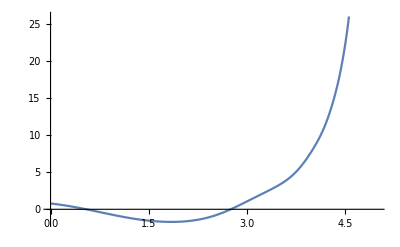

```mathematica
T = m*(l-α*t)^2 *ϕdot^2/2;
U = m*g*(l - (l -α*t)*Cos[ϕ]);
L = T- U;
vals = {ϕ-> ϕ[t], ϕdot -> ϕ'[t]};

dLdphi = D[L, ϕ]/.vals;
dLdphidot = D[L, ϕdot]/.vals;

eq3 = dLdphi - D[dLdphidot, t]==0;
eq3 = FullSimplify[eq3]

l = 5;
α = 1;
g = 9.8;
m = 1;
eq3 = m (l-t α) (g*Sin[ϕ[t]]-2 α ϕ'[t]+(l-t α) ϕ''[t])==0;

s = NDSolve[{eq3, ϕ[0]==Pi/4, ϕ'[0]==-1 }, ϕ, {t, 0, 5}]
Plot[Evaluate[ϕ[t]/.s], {t, 0, 5}]
```